This notebook is written by Christoph Koutschan and Elaine Wong and accompanies the paper: 
"Walsh functions, scrambled $(0,m,s)$-nets, and negative covariance: applying symbolic computation to quasi-Monte Carlo integration"  by Jaspar Wiart and Elaine Wong. 
The main reason to publish these computations is to provide a rigorous proof for Lemma 15 in the paper (Part 4). However, we feel there is some value to include the guessing and evidence for our conjecture, since it was a part of the research process (Parts 2 and 5). To run this notebook, the following packages must be downloaded (please see references for links) and placed in the correct folders.

```mathematica
SetDirectory[NotebookDirectory[]];
<<RISC`HolonomicFunctions`;
<<RISC`Guess`;
```

HolonomicFunctions Package version 1.7.3 (21-Mar-2017)
written by Christoph Koutschan
Copyright Research Institute for Symbolic Computation (RISC),
Johannes Kepler University, Linz, Austria

--> Type  ?HolonomicFunctions  for help.

Guess Package version 0.52
written by Manuel Kauers
Copyright Research Institute for Symbolic Computation (RISC),
Johannes Kepler University, Linz, Austria

```mathematica
Sigma`Summation`Objects`S=SigmaS;
Sigma`Summation`SumProducts`CreativeTelescoping=SigmaCT;
Quiet[Import["Sigma.m"],General::shdw]
Remove[Sigma`Summation`Objects`S,Sigma`Summation`SumProducts`CreativeTelescoping];
```

Sigma - A summation package by Carsten Schneider — © RISC —  V 2.01 (May 12, 2016)  Help

## Part 0: Definitions

```mathematica
(* Definition 10.2 (note that the dimension s is implicit). *)
psi[b_,c_,r_]:=-(1-b)^(1-r)*Sum[(-b)^i*Binomial[r-1,i],{i,0,r-1-c}];
(* Generalized Decay Function in Lemma 12. *)
decay[a_,b_,k_,r_,x_]:=a^r(b x)^k
(* Main Polynomial: Equation 6 in Lemma 12. *)
poly[a_,b_,m_,s_]:=Sum[Sum[Binomial[s,r]*Binomial[k-1,r-1]*psi[b,Max[k-m,0],r]*decay[a,b,k,r,x],{r,s}],{k,m+s-1}]
(* Main Polynomial: Separated terms without Max function *)
polyfirst[a_,b_,m_,s_]:=-Sum[Sum[Binomial[s,r]*Binomial[k-1,r-1]*decay[a,b,k,r,x],{r,s}],{k,m+s-1}]
polyinner[b_,k_,m_,r_]:=Sum[(-b)^(i)*Binomial[r-1,i],{i,r-k+m,r-1}]
polylast[a_,b_,m_,s_]:=-Sum[Sum[Binomial[s,r]*Binomial[k-1,r-1]*(-(1-b)^(1-r))*polyinner[b,k,m,r]*decay[a,b,k,r,x],{r,s}],{k,m+1,m+s-1}];
```

## Part 1: Numerical Checks and Intuition for a=(b-1)/b

```mathematica
(* Experimental confirmation that poly = polyfirst + polylast. *)
Table[Together[poly[(b-1)/b,b,m,s]-polyfirst[(b-1)/b,b,m,s]-polylast[(b-1)/b,b,m,s]],{m,30},{s,30}]//Flatten//Union
```

{0}

#### Section 5 Figures for a=(b-1)/b

```mathematica
(* Color Setup *)
primes={};
Do[If[PrimeQ[i],primes=Append[primes,i]],{i,100}]
graylist=Most[Table[GrayLevel[i],{i,0,0.8,0.1}]];
bluelist=Most[Table[ColorData["BlueGreenYellow"][i],{i,0,0.8,0.1}]];
colorblend=Reverse[Flatten[Append[graylist,bluelist//Reverse]]];
```

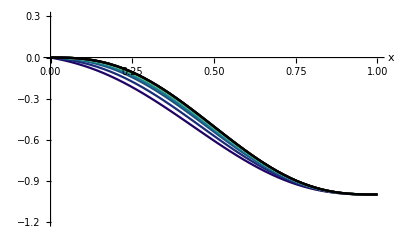

```mathematica
(* Figure 4a: b varies, a=(b-1)/b, m=3, s=3, scaling factor=(b^3-1)^(-1) *)
mtest=3; stest=3; 
polylist=Table[(b^mtest-1)^(-1)*poly[(b-1)/b,b,mtest,stest],{b,primes[[1;;16]]}];
Plot[polylist,{x,0,1},PlotRange->{-1.2,0.3},AxesLabel->{"x"},PlotStyle->colorblend, AxesStyle->GrayLevel[0.3]]
```

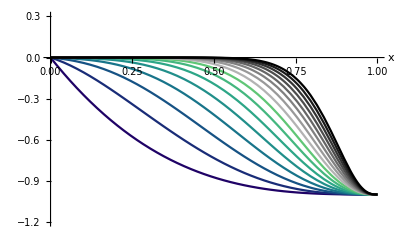

```mathematica
(* Figure 4b: m varies, b=3, a=2/3, s=3, scaling factor=(3^m-1)^(-1) *)
btest=3; atest=(btest-1)/btest; stest=3; 
polylist=Table[(btest^m-1)^(-1)*poly[atest,btest, m, stest],{m,16}];
Plot[polylist,{x,0,1},PlotRange->{-1.2,0.3},AxesLabel->{"x"},PlotStyle->colorblend, AxesStyle->GrayLevel[0.3]]
```

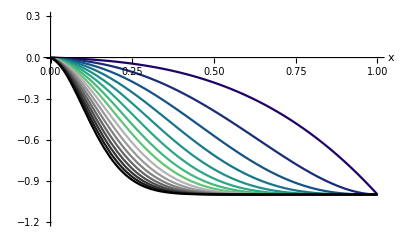

```mathematica
(* Figure 4c: s varies, b=3, a=2/3, m=3, scaling factor=1/26 *)
btest=3; atest=(btest-1)/btest; mtest=3; 
polylist=Table[(btest^mtest-1)^(-1)*poly[atest,btest, mtest, s],{s,16}];
Plot[polylist,{x,0,1},PlotRange->{-1.2,0.3},AxesLabel->{"x"},PlotStyle->colorblend, AxesStyle->GrayLevel[0.3]]
```

## Part 2: Guess a Recurrence for the Polynomial in Lemma 12, Eq (6)

```mathematica
(* We generate data necessary for guessing in all four variables. *)
(* We impose what we believe the shape of the recurrence to be, and if such a recurrence exists, the function will find one. *)
list=(Table[poly[(b-1)/b,b,m,s],{x,2,10},{b,2,10},{m,10},{s,10}]//Together);
rec=GuessMultRE[list,{c[x,b,m,s],c[x,b,m,s+1],c[x,b,m,s+2],c[x,b,m,s+3]},{x,b,m,s},4,StartPoint->{2,2,1,1}][[1]]
```

(1+m+s) (-1+x)^2 c[x,b,m,s]-(-1+x) (-4-2 m-3 s+x+b x+m x+b m x+s x+b s x) c[x,b,m,1+s]+(5+m+3 s-3 x-3 b x-m x-b m x-2 s x-2 b s x+b x^2+b m x^2+b s x^2) c[x,b,m,2+s]+(2+s) (-1+b x) c[x,b,m,3+s]

```mathematica
(* Since the recurrence only depends on s, we make some subsitutions so that it looks nicer for printing. *)
guessrec=rec/.(Thread[c[x,b,m,s+#]->c[s+#]]&/@(Range[4]-1))
```

(1+m+s) (-1+x)^2 c[s]-(-1+x) (-4-2 m-3 s+x+b x+m x+b m x+s x+b s x) c[1+s]+(5+m+3 s-3 x-3 b x-m x-b m x-2 s x-2 b s x+b x^2+b m x^2+b s x^2) c[2+s]+(2+s) (-1+b x) c[3+s]

## Part 3: Solve the Recurrence and Simplify

#### a) Solve Recurrence

```mathematica
(* We solve the recurrence and find that we are lucky to get a non-trivial solution.*)
recsol=SolveRecurrence[rec==0,c[s]]
```

{{0,1},{0,((-1+b x) ((-1+x)/(-1+b x))^(s_.))/((-1+b) x)},{0,((1-b x) ((-1+x)/(-1+b x))^(s_.) ((∑^.)_(ι_1=1)^s(∏^.)_(ι_2=1)^ι_1(-1/ι_2(-1+b x) (-1+m+ι_2))))/((-1+b) x)+((-1+b x) ((∑^.)_(ι_1=1)^s((-1+x)/(-1+b x))^(ι_1_.) (∏^.)_(ι_2=1)^ι_1(-1/ι_2(-1+b x) (-1+m+ι_2))))/((-1+b) x)},{1,0}}

```mathematica
(* Combine all solutions together with initial values using the following command. *)
?FindLinearCombination
```

FindLinearCombination[recSol,DATA,n,r, MinInitialValue->n0] tries to compute a linear comination of recSol such that it equals to the input DATA for all integers n>=n0; exactly r initial values are taken into consideration in order to accomplish this task (if r is the order of the recurrence, the correctness of the computation follows).  By default MinInitialValues is set to Automatic: the starting point n0 is chosen automatically. DATA might be an expression that can be evaluated in n. Alternatively, DATA might be of the form {s,{a1,a2,a3,...}} where {a1,a2,...} are the initial values for n=s,s+1,s+2,... for some integer s; if DATA is of the form {a1,a2,...}, it is assumed that s=0. See also the option Substitution.

```mathematica
(* We use the separated version of the polynomial (so that Mathematica doesn't have to deal with cases from the Max function). *)
inival=Table[PowerExpand[FunctionExpand[polyfirst[(b-1)/b,b,m,i]]+polylast[(b-1)/b,b,m,i]]//Simplify,{i,3}];
recsol=Together[FindLinearCombination[recsol,{1,inival},s,3,MinInitialValue->1]]
```

1-b^(m_.) x^(m_.)-((-1+x)/(-1+b x))^(s_.)+b^(m_.) x^(m_.) ((-1+x)/(-1+b x))^(s_.)+b^(m_.) x^(m_.) ((-1+x)/(-1+b x))^(s_.) ((∑^.)_(ι_1=1)^s(∏^.)_(ι_2=1)^ι_1(-((-1+b x) (-1+m+ι_2))/ι_2))-b^(m_.) x^(m_.) ((∑^.)_(ι_1=1)^s((-1+x)/(-1+b x))^(ι_1_.) (∏^.)_(ι_2=1)^ι_1(-((-1+b x) (-1+m+ι_2))/ι_2))

#### b) Simplify to a Closed Form

These were deduced by hand using identities from the DLMF. However, we use Mathematica to numerically confirm the expressions to give us confidence.

```mathematica
(* Step 1: We try to make the solution look nicer by replacing the notation from Sigma to the more standard Mathematica notation. *)
(* This gives us expression (8) *)
simp1=recsol/.Sigma`Summation`Objects`Private`MyPower->Power/.Sigma`Summation`Objects`Private`MyProduct->Product/.Sigma`Summation`Objects`Private`i[1]->i/.Sigma`Summation`Objects`Private`MySum->Sum/.Sigma`Summation`Objects`Private`i[2]->j;
simp1=FunctionExpand[simp1]
```

1-b^m x^m-((-1+x)/(-1+b x))^s+b^m x^m ((-1+x)/(-1+b x))^s+b^m (-1+x^m)+b^m x^m ((-1+x)/(-1+b x))^s (-1+(b x)^-m)-(b^m x^m (1-b x)^(1+s) ((-1+x)/(-1+b x))^s Gamma[1+m+s] Hypergeometric2F1[1,1+m+s,2+s,1-b x])/(Gamma[m] Gamma[2+s])+(b^m (1-x)^(1+s) Gamma[1+m+s] Hypergeometric2F1[1-m,1+s,2+s,1-x])/(Gamma[m] Gamma[2+s])

```mathematica
(* Step 2: Simplify Gammas and use a DLMF identity to convert the 2F1's into the regularized beta functions. *)
(* We compare with simp1 to make sure we are on the right track. *) 
simp2=(1-(b x)^m)-(1-(b x)^m)((-1+x)/(-1+b x))^s+(b x)^m(x^-m (-1+x^m) +x^-m BetaRegularized[1-x,s+1,m])+(b x)^m((-1+x)/(-1+b x))^s((b x)^(-m)-1-(b x)^(-m)BetaRegularized[1-b x ,s+1,m])
Table[FullSimplify[simp1-simp2],{b,2,4},{m,4},{s,4}]
```

1-(b x)^m-((-1+x)/(-1+b x))^s (1-(b x)^m)+(b x)^m (x^-m (-1+x^m)+x^-m BetaRegularized[1-x,1+s,m])+(b x)^m ((-1+x)/(-1+b x))^s (-1+(b x)^-m-(b x)^-m BetaRegularized[1-b x,1+s,m])

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
(* Step 3: Use symmetry of the normalized beta function. *)
simp3= (1- b^m x^m)-(1-b^m x^m)((-1+x)/(-1+b x))^s+b^m x^m ((x^m-1) x^(-m)+x^(-m)(1-BetaRegularized[x,m,s+1]))+ b^m x^m ((-1+x)/(-1+b x))^s((b x)^(-m)-1-(b x)^(-m)BetaRegularized[1-b x ,s+1,m])
Table[FullSimplify[simp2-simp3],{b,2,4},{m,4},{s,4}]
```

1-b^m x^m-((-1+x)/(-1+b x))^s (1-b^m x^m)+b^m x^m (x^-m (-1+x^m)+x^-m (1-BetaRegularized[x,m,1+s]))+b^m x^m ((-1+x)/(-1+b x))^s (-1+(b x)^-m-(b x)^-m BetaRegularized[1-b x,1+s,m])

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
(* Step 4: We simplify and put everything together and this is our Q polynomial as defined in the paper. *)
Q[b_,m_,s_]:=1-b^m BetaRegularized[x,m,s+1]-((-1+x)/(-1+b x))^s BetaRegularized[1-b x,s+1,m]
Table[FullSimplify[simp3-Q[b,m,s]],{b,2,4},{m,4},{s,4}]
```

## Part 4: Rigorously Deduce a Recurrence for the Polynomial in Eq (6): Proof of Lemma 15

This section proves Lemma 15 in the paper.

```mathematica
(* This was derived in Part 2 but we reload it here for convenience. *)
guessrec=(1+m+s) (-1+x)^2 c[s]-(-1+x) (-4-2 m-3 s+x+b x+m x+b m x+s x+b s x) c[1+s]+(5+m+3 s-3 x-3 b x-m x-b m x-2 s x-2 b s x+b x^2+b m x^2+b s x^2) c[2+s]+(2+s) (-1+b x) c[3+s];
(* For testing purposes and sanity checks, we will use the following substitutions. *)
subs={b->31,m->15,x->5/7};
checksubs={30/31, 31, 15,s};
```

#### Creative Telescoping for polyfirst

```mathematica
(* summand1 *)
f[s_,k_,r_]:=Binomial[s,r]*Binomial[k-1,r-1]*decay[(b-1)/b,b,k,r,x];
(* innersum *)
F1[s_,k_]:=Sum[f[s,k,r],{r,1,s}];
(* outersum *)
G1[s_]:=Sum[F1[s,k],{k,1,m+s-1}];
```

INNER SUM

```mathematica
{Pinner1,Qinner1}=CreativeTelescoping[f[s,k,r],S[r]-1,{S[k],S[s]}];
(* Because the inner sum has natural boundaries (in particular, the summands evaluate to zero), the telescopers will annihilate the inner sum. *)
anninner1=Pinner1;
(* The support gives an idea of the operators that we are dealing with in our annihilating ideal. *)
Support[anninner1]
```

{{S_k,S_s,1},{S_s^2,S_s,1}}

```mathematica
(* A quick check (with specialized values) shows that our anninner1 is correct. *)
Table[ApplyOreOperator[#,FFa[s,k]]&/@anninner1,{s,30}];
((%/.FFa->F1/.subs/.k->18)//Flatten//Union)==={0}
```

True

OUTER SUM

```mathematica
{Pouter1,Qouter1}=CreativeTelescoping[anninner1,S[k]-1,{S[s]}];
```

Symbolic Computation : Here we deal with unnatural boundaries and the fact that the telescoper does not commute with the sum and make the appropriate adjustments

```mathematica
(* We first apply the certificates and then determine the collapsing sum (up to k=m+s-1). *)
outercert1=With[{delta=ApplyOreOperator[Qouter1[[1]],F1[s,k]]},(delta/.k->(s+m))-(delta/.k->1)]; 
(* Next, we determine the annihilator of the collapsed sum and extra stuff that was added to Sum[P*F[s,k],{k,1,m+s-1}] so that what remains is P*Sum[F[s,k],{k,1,m+s-1}]. *)
outerstuff1=(1-b x)F1[s+1,m+s];
(* The inhomogenous part is the combination of stuff we want to remove and the telescoped sum. *)
inhom1=FunctionExpand[-outerstuff1+outercert1];
```

It is important to note that inhom1 can be simplified and rewritten so that we can use the closure property of applying an operator.

```mathematica
inhom1first=inhom1[[1;;2]];
inhom1last=inhom1[[3;;5]];
expr=((-1+b) (1+m+s)/(b^2 x))*(b x)^(1+m+s) Hypergeometric2F1[1-s,-m-s,2,(-1+b)/b]+((-1+b) (-m-b s)/b^2)*(b x)^(m+s) Hypergeometric2F1[1-s,1-m-s,2,(-1+b)/b]+((-1+b) (1+s) (-1+b x)/b)*(b x)^(m+s) Hypergeometric2F1[1-m-s,-s,2,(-1+b)/b];
FullSimplify[expr-inhom1last]===0
(* We rewrite expr as a combination of some shifts (by observation). *)
hg[s_,m_]:=(b x)^(m+s)*Hypergeometric2F1[1-s,2-m-s,2,(b-1)/b]
pf1=HoldForm[(-1+b)(1+m+s)/(b^2 x * b x )];
pf2=HoldForm[(-1+b)(-m-b s)/(b^2 * b x)];
pf3=HoldForm[(-1+b)(1+s)(-1+b x)/(b *b x)];
op=pf1 S[m]^2+pf2 S[m]+pf3 S[s];
applyop=ReleaseHold[ApplyOreOperator[op,hg[s,m]]];
```

True

This allows us to compute the annihilator for inhom1 by computing the separate annihilators and applying the closure property.

```mathematica
anninhom1first=Annihilator[inhom1first,{S[s]}];
anninhom1last=DFiniteOreAction[Annihilator[hg[s,m],{S[m],S[s]}],ReleaseHold[op]];
R1=DFinitePlus[anninhom1first,{ToOrePolynomial[anninhom1last[[2]],OreAlgebra[S[s]]]}];
(* We now finally have a good annihilator for polyfirst. *)
annouter1=((#**Pouter1[[1]])&/@R1); 
(* The support gives an idea of the operators that we are dealing with in our annihilating ideal. *)
Support[annouter1]
```

{{S_s^4,S_s^3,S_s^2,S_s,1}}

```mathematica
(* Another quick check confirms that we are on the right track. *)
Table[ApplyOreOperator[#,(polyfirst@@checksubs)/.x->5/7]&/@annouter1,{s,30}];
(%/.subs//Flatten//Union)==={0}
```

True

#### Creative Telescoping for polylast

```mathematica
(* summand2 *)
h[s_,k_,r_]:=Binomial[s,r]*Binomial[k-1,r-1]*(-(1-b)^(1-r))*polyinner[b,k,m,r]*decay[(b-1)/b,b,k,r,x]; 
(* innersum *)
H[s_,k_]:=Sum[h[s,k,r],{r,1,s}];
(* outersum *)
G2[s_]:=Sum[H[s,k],{k,m+1,m+s-1}];
```

INNER SUM

```mathematica
{Pinner2,Qinner2}=CreativeTelescoping[h[s,k,r],S[r]-1,{S[k],S[s]}];
(* Because the inner sum has natural boundaries (in particular, the summands evaluate to zero), the telescopers will annihilate the inner sum. *)
anninner2=Pinner2;
(* The support gives an idea of the operators that we are dealing with in our annihilating ideal. *)
Support[anninner2]
```

{{S_s^2,S_k,S_s,1},{S_k S_s,S_k,1},{S_k^2,S_k,S_s,1}}

```mathematica
(* Always good to keep checking... *)
Table[ApplyOreOperator[#,HH[s,k]]&/@anninner2,{s,30}];
((%/.HH->H/.subs/.k->18)//Flatten//Union)==={0}
```

True

OUTER SUM

```mathematica
(* Timing[{Pouter2,Qouter2}=CreativeTelescoping[anninner2,S[k]-1,{S[s]}];] *)
(* This took about 70 seconds so we save it for future use. *)
(* {Pouter2,Qouter2}>>"qouter2.m" *)
{Pouter2,Qouter2}=Import["ctouter2.m"]; 
(* We can extract coefficients from the telescoper, which will be used later. *)
Pouter2coeff=OrePolynomialListCoefficients[Pouter2[[1]]];
```

Symbolic Computation I: Here we deal with the fact that the telescoper does not commute with the sum and make the appropiate adjustments.

```mathematica
(* We first apply the certificates and then determine the collapsing sum (up to k=m+s-1). *)
outercert2=With[{delta=ApplyOreOperator[Qouter2,HH[s,k]]},(delta/.k->(m+s))-(delta/.k->(m+1))];
(* Next we determine the stuff that must be removed to take into account the extra shifts when moving the telescopers outside of the sum. *)
outerstuff2=Total[Pouter2coeff[[1;;3]]*Table[Sum[HH[s+i,k],{k,m+s,m+s+i-1}],{i,3,1,-1}]];
(* The inhomogenous part is the combination of stuff we want to remove and the telescoped sum. *)
inhom2=-outerstuff2+outercert2;
```

Symbolic Computation II: Here we try to avoid Mathematica's use of 2F1s and DifferenceRoots by rewriting all the inhomogenous parts as an operator.

```mathematica
(* We first note that the pieces that don't have 2F1s evaluate to 0: this corresponds to evaluating the sum with the certificates at the lower boundary. *)
posfree=Position[FreeQ[#,Hypergeometric2F1]&/@(List@@inhom2[[1]]/.HH->H),True]//Flatten;
Last/@(List@@inhom2[[1,posfree]])
{inhom2[[1,posfree]]/.HH->H//Cancel//FunctionExpand};
(* We remove those zero pieces and proceed to determine an annihilator for the rest of inhom2. *)
inhom2rest=(inhom2[[1,Complement[Range[9],posfree]]]);
(* We first rewrite all these parts as an operator (by observation) *)
newop=Qouter2-Sum[Coefficient[Pouter2[[1]],S[s],i]**S[s]^i**Sum[S[k]^j,{j,0,i-1}],{i,3}];
(* Check! *)
Together[inhom2rest-ApplyOreOperator[newop,HH[s,k]]/.k->(m+s)]
```

{HH[s,1+m],HH[s,2+m],HH[1+s,1+m]}

{0}

And now comes the big computation.

```mathematica
(* Timing[R2act=DFiniteOreAction[anninner2,newop];] *)
(* The above took 619 seconds. *)
(* Timing[R2=DFiniteSubstitute[R2act,{k->(m+s)}];] *)
(* This above took 107860 seconds!! So we save it. *)
(* R2>>"ctR2.m"; *)
R2=Import["ctR2.m"];
annouter2={R2[[1]]**Pouter2[[1]]};
(* The support gives an idea of the operators that we are dealing with in our annihilating ideal. *)
Support[annouter2]
```

{{S_s^5,S_s^4,S_s^3,S_s^2,S_s,1}}

```mathematica
(* Our final small check *)
Table[ApplyOreOperator[#,(polylast@@checksubs)/.x->5/7]&/@annouter2,{s,30}];
((%/.subs)//Flatten//Union)==={0}
```

True

#### Combine above computations to get a recurrence for poly (Eq 6)

Because the sum of two holonomic functions is still holonomic, we apply the corresponding closure property to get the annihilator for poly.

```mathematica
annfinal=DFinitePlus[annouter1,annouter2];
Support[annfinal]
```

{{S_s^5,S_s^4,S_s^3,S_s^2,S_s,1}}

```mathematica
(* Check *)
Table[ApplyOreOperator[annfinal,PP[30/31,31,15,s]],{s,10}];
((%/.PP->poly/.subs)//Flatten//Union)==={0}
```

True

We convert now our guessrec to an OrePolynomial so that we can compare.

```mathematica
guessrecpoly=ToOrePolynomial[guessrec,c[s]];
```

```mathematica
(* Check *)
Table[ApplyOreOperator[guessrecpoly,PP[30/31,31,15,s]],{s,10}];
((%/.PP->poly/.subs)//Flatten//Union)==={0}
```

True

And the last step: is our computed recurrence a left multiple of the guessed one? Yes, yes it is!

```mathematica
OreReduce[annfinal[[1]], {guessrecpoly}]
```

0

```mathematica
(* We check to see that the recurrences produces the same result given a finite number of initial values. *)
annrec=ApplyOreOperator[annfinal[[1]],c[s]];
numic=6;len=12;
(* Initial conditions from poly. *)
sublist=Thread[Table[c[i],{i,numic}]->Table[polyfirst[(b-1)/b,b,m,s]+polylast[(b-1)/b,b,m,s],{s,numic}]];
subguess=sublist[[1;;numic-2]];
(* Use both recurrences to generate lists up to 15 terms using the initial conditions. *)
Do[
subguess=Append[subguess,Solve[guessrec==0,c[s+3]][[1]]/.s->s0/.subguess]//Flatten;sublist=Append[sublist,Solve[annrec==0,c[s+5]][[1]]/.s->s0/.sublist]//Flatten,
{s0,2,len}]
(* Compare *)
Timing[Union[Together[Last/@subguess-Last/@sublist[[1;;Length[subguess]]]]]]
```

{218.568,{0}}

## Part 5: Experiments for the General Case

We comment that a = (b-1) / b is a bit special.

```mathematica
(* In such a case, we have a special monotonicity property that holds when x=1. *)
Table[CylindricalDecomposition[{0≤a≤1,D[poly[a,b,m,s]/.x->1,a]≥0},{a}],{b,primes[[1;;16]]},{m,5},{s,3,3}]//Flatten//Union
```

{a==1/2,a==2/3,a==4/5,a==6/7,a==10/11,a==12/13,a==16/17,a==18/19,a==22/23,a==28/29,a==30/31,a==36/37,a==40/41,a==42/43,a==46/47,a==52/53}

#### Section 6 Figures

However, we can still provide some experimental evidence that the result holds for  different values of a. We will use the same color setup.

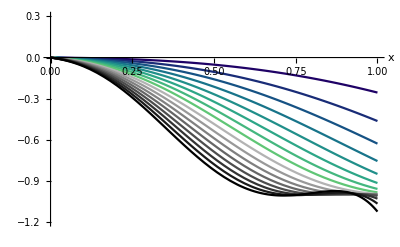

```mathematica
(* Figure 5: a varies, b=3, m=3, s=3, scaling factor=1/26 *)
btest=3;  mtest=3; stest=3; 
polylist=Table[(btest^mtest-1)^(-1)*poly[a,btest,mtest,stest],{a,1/16,1,1/16}];
Plot[polylist,{x,0,1},PlotRange->{-1.2,0.3},AxesLabel->{"x"},PlotStyle->colorblend, AxesStyle->GrayLevel[0.3]]
```

For a=1 (the next logical choice for decay), we observe some erratic behavior in our domain. In such a situation, a recurrence of order 4 was found, but only with trivial solutions.

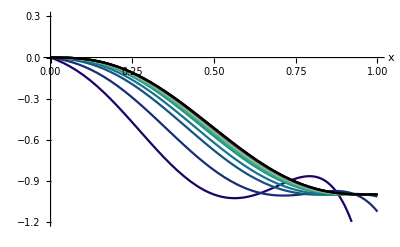

```mathematica
(* Figure 6a: b varies, a=1, m=3, s=3, scaling factor=(b^3-1)^(-1) *)
atest=1;mtest=3; stest=3; 
polylist=Table[(b^mtest-1)^(-1)*poly[atest,b,mtest,stest],{b,primes[[1;;16]]}];
Plot[polylist,{x,0,1},PlotRange->{-1.2,0.3},AxesLabel->{"x"},PlotStyle->colorblend, AxesStyle->GrayLevel[0.3]]
```

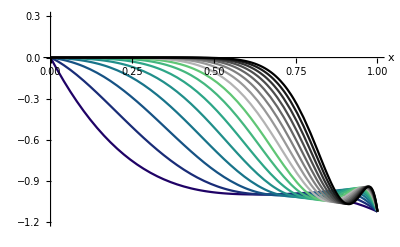

```mathematica
(* Figure 6b: m varies, a=1, b=3, s=3, scaling factor=(3^m-1)^(-1) *)
atest=1;btest=3; stest=3; 
polylist=Table[(btest^m-1)^(-1)*poly[atest,btest,m,stest],{m,16}];
Plot[polylist,{x,0,1},PlotRange->{-1.2,0.3},AxesLabel->{"x"},PlotStyle->colorblend, AxesStyle->GrayLevel[0.3]]
```

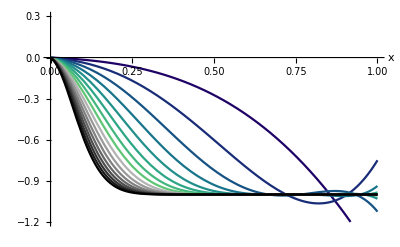

```mathematica
(* Figure 6c: s varies, a=1, b=3, m=3, scaling factor=1/26 *)
atest=1;btest=3; mtest=3; 
polylist=Table[(btest^mtest-1)^(-1)*poly[atest,btest,mtest,s],{s,16}];
Plot[polylist,{x,0,1},PlotRange->{-1.2,0.3},AxesLabel->{"x"},PlotStyle->colorblend, AxesStyle->GrayLevel[0.3]]
```

#### A Possible Recurrence for general a

In fact, for general a, the guessed recurrence produced only produced trivial results, and this did not motivate us to pursue the investigation further using this technique.

```mathematica
(* We generate data necessary for guessing in all four variables and leave a symbolic. *)
(* We impose what we believe the shape of the recurrence to be, and if such a recurrence exists, the function will find one. *)
list=(Table[poly[a,b,m,s],{x,2,15},{b,2,15},{m,15},{s,15}]//Together);
reca=GuessMultRE[list,{c[x,b,m,s],c[x,b,m,s+1],c[x,b,m,s+2],c[x,b,m,s+3],c[x,b,m,s+4]},{x,b,m,s},6,StartPoint->{2,2,1,1}][[1]]
```

-(1-b+a b) (1+s) (1-b+a b x) (1-b x+a b x) c[x,b,m,s]+(6-12 b+4 a b+6 b^2-4 a b^2-a b m+a b^2 m+4 s-8 b s+3 a b s+4 b^2 s-3 a b^2 s-6 b x+9 a b x+12 b^2 x-18 a b^2 x+5 a^2 b^2 x-6 b^3 x+9 a b^3 x-3 a^2 b^3 x+a b m x-a^2 b^2 m x-a b^3 m x+a^2 b^3 m x-4 b s x+6 a b s x+8 b^2 s x-12 a b^2 s x+4 a^2 b^2 s x-4 b^3 s x+6 a b^3 s x-2 a^2 b^3 s x-4 a b^2 x^2+3 a^2 b^2 x^2+4 a b^3 x^2-5 a^2 b^3 x^2+a^3 b^3 x^2-a b^2 m x^2+a^2 b^2 m x^2+a b^3 m x^2-a^2 b^3 m x^2-3 a b^2 s x^2+2 a^2 b^2 s x^2+3 a b^3 s x^2-4 a^2 b^3 s x^2+a^3 b^3 s x^2) c[x,b,m,1+s]+(-12+24 b-5 a b-12 b^2+5 a b^2+2 a b m-2 a b^2 m-6 s+12 b s-3 a b s-6 b^2 s+3 a b^2 s+12 b x-12 a b x-24 b^2 x+24 a b^2 x-3 a^2 b^2 x+12 b^3 x-12 a b^3 x+2 a^2 b^3 x-2 a b m x+a^2 b^2 m x+2 a b^3 m x-a^2 b^3 m x+6 b s x-6 a b s x-12 b^2 s x+12 a b^2 s x-2 a^2 b^2 s x+6 b^3 s x-6 a b^3 s x+a^2 b^3 s x+5 a b^2 x^2-2 a^2 b^2 x^2-5 a b^3 x^2+3 a^2 b^3 x^2+2 a b^2 m x^2-a^2 b^2 m x^2-2 a b^3 m x^2+a^2 b^3 m x^2+3 a b^2 s x^2-a^2 b^2 s x^2-3 a b^3 s x^2+2 a^2 b^3 s x^2) c[x,b,m,2+s]+(-1+b) (-10+10 b-2 a b+a b m-4 s+4 b s-a b s+10 b x-5 a b x-10 b^2 x+5 a b^2 x-a b m x-a b^2 m x+4 b s x-2 a b s x-4 b^2 s x+2 a b^2 s x+2 a b^2 x^2+a b^2 m x^2+a b^2 s x^2) c[x,b,m,3+s]+(-1+b)^2 (3+s) (-1+b x) c[x,b,m,4+s]

```mathematica
(* Since the recurrence only depends on s, we make some subsitutions so that it looks nicer for printing. *)
guessreca=reca/.(Thread[c[x,b,m,s+#]->c[s+#]]&/@(Range[5]-1))
```

-(1-b+a b) (1+s) (1-b+a b x) (1-b x+a b x) c[s]+(6-12 b+4 a b+6 b^2-4 a b^2-a b m+a b^2 m+4 s-8 b s+3 a b s+4 b^2 s-3 a b^2 s-6 b x+9 a b x+12 b^2 x-18 a b^2 x+5 a^2 b^2 x-6 b^3 x+9 a b^3 x-3 a^2 b^3 x+a b m x-a^2 b^2 m x-a b^3 m x+a^2 b^3 m x-4 b s x+6 a b s x+8 b^2 s x-12 a b^2 s x+4 a^2 b^2 s x-4 b^3 s x+6 a b^3 s x-2 a^2 b^3 s x-4 a b^2 x^2+3 a^2 b^2 x^2+4 a b^3 x^2-5 a^2 b^3 x^2+a^3 b^3 x^2-a b^2 m x^2+a^2 b^2 m x^2+a b^3 m x^2-a^2 b^3 m x^2-3 a b^2 s x^2+2 a^2 b^2 s x^2+3 a b^3 s x^2-4 a^2 b^3 s x^2+a^3 b^3 s x^2) c[1+s]+(-12+24 b-5 a b-12 b^2+5 a b^2+2 a b m-2 a b^2 m-6 s+12 b s-3 a b s-6 b^2 s+3 a b^2 s+12 b x-12 a b x-24 b^2 x+24 a b^2 x-3 a^2 b^2 x+12 b^3 x-12 a b^3 x+2 a^2 b^3 x-2 a b m x+a^2 b^2 m x+2 a b^3 m x-a^2 b^3 m x+6 b s x-6 a b s x-12 b^2 s x+12 a b^2 s x-2 a^2 b^2 s x+6 b^3 s x-6 a b^3 s x+a^2 b^3 s x+5 a b^2 x^2-2 a^2 b^2 x^2-5 a b^3 x^2+3 a^2 b^3 x^2+2 a b^2 m x^2-a^2 b^2 m x^2-2 a b^3 m x^2+a^2 b^3 m x^2+3 a b^2 s x^2-a^2 b^2 s x^2-3 a b^3 s x^2+2 a^2 b^3 s x^2) c[2+s]+(-1+b) (-10+10 b-2 a b+a b m-4 s+4 b s-a b s+10 b x-5 a b x-10 b^2 x+5 a b^2 x-a b m x-a b^2 m x+4 b s x-2 a b s x-4 b^2 s x+2 a b^2 s x+2 a b^2 x^2+a b^2 m x^2+a b^2 s x^2) c[3+s]+(-1+b)^2 (3+s) (-1+b x) c[4+s]

```mathematica
(* Solving the recurrence produces only trivial solutions. *)
```

```mathematica
recsola=SolveRecurrence[guessreca==0,c[s]]
```

{{0,1},{0,((-1+b x) ((-1+b x-a b x)/(-1+b x))^(s_.))/(a b x)},{1,0}}

## Export to PDF

```mathematica
Export["nets_papercomputations.pdf",Get["nets_papercomputations.nb"]/.ButtonBox[__]->" Help"];
```